```mathematica
ListPointPlot3D[{xFacePosS,xFacePos},PlotStyle->{Blue,Red}]
```

```mathematica
allPoints=Join[xFacePosS,xFacePos];
zero=allPoints[[lookupface[3,1,3]]];
For[ii=1,ii<=Length[allPoints],ii++,
allPoints[[ii]]=allPoints[[ii]]-zero;
]
fancyFunction[x_,y_,z_]=  (y-5)^2;
realLaplacian[x_,y_,z_]=Laplacian[fancyFunction[x,y,z],{x,y,z}];
allVals=Table[fancyFunction[allPoints[[ii,1]],allPoints[[ii,2]],allPoints[[ii,3]]],{ii,1,Length[allPoints]}];

(*16/21 Subscript[xf, 5,4,5]/delta^2+16/21 Subscript[xf, 5,4,6]/delta^2+Subscript[XF, 2,1,3]/delta^2+20/21 Subscript[XF, 3,1,2]/delta^2-46/7 Subscript[XF, 3,1,3]/delta^2+20/21 Subscript[XF, 3,1,4]/delta^2+8/7 Subscript[XF, 3,2,3]/delta^2+Subscript[XF, 4,1,3]/delta^2*)
Subscript[xf, 5,3,5]/(27 Δ^2)+Subscript[xf, 5,3,6]/(27 Δ^2)+(32 Subscript[xf, 5,4,5])/(27 Δ^2)+(32 Subscript[xf, 5,4,6])/(27 Δ^2)+Subscript[XF, 2,1,3]/Δ^2+(713 Subscript[XF, 3,1,2])/(729 Δ^2)-(4069 Subscript[XF, 3,1,3])/(729 Δ^2)+(713 Subscript[XF, 3,1,4])/(729 Δ^2)+(8 Subscript[XF, 3,2,3])/(9 Δ^2)+Subscript[XF, 4,1,3]/Δ^2
```

(xf_(5,3,5))/(27 Δ^2)+(xf_(5,3,6))/(27 Δ^2)+(32 xf_(5,4,5))/(27 Δ^2)+(32 xf_(5,4,6))/(27 Δ^2)+(XF_(2,1,3))/Δ^2+(713 XF_(3,1,2))/(729 Δ^2)-(4069 XF_(3,1,3))/(729 Δ^2)+(713 XF_(3,1,4))/(729 Δ^2)+(8 XF_(3,2,3))/(9 Δ^2)+(XF_(4,1,3))/Δ^2

```mathematica
discreteLap=allVals[[lookupfaceS[5,3,5]]]/(27.0 delta^2)+ allVals[[lookupfaceS[5,3,6]]]/(27 delta^2)+(32allVals[[lookupfaceS[5,4,5]]])/(27 delta^2)+ (32allVals[[lookupfaceS[5,4,6]]])/(27 delta^2)+allVals[[lookupface[2,1,3]]]/delta^2+ (713 allVals[[lookupface[3,1,2]]])/(729 delta^2)-4069/729 allVals[[lookupface[3,1,3]]]/delta^2+ 713/729 allVals[[lookupface[3,1,4]]]/delta^2+ 8/9 allVals[[lookupface[3,2,3]]]/delta^2+allVals[[lookupface[4,1,3]]]/delta^2
(*allVals[[lookupface[2,1,3]]]/delta^2-2 allVals[[lookupface[3,1,3]]]/delta^2+ allVals[[lookupface[4,1,3]]]/delta^2
allVals[[lookupfaceS[5,4,5]]]/delta^2+ allVals[[lookupfaceS[5,4,6]]]/delta^2-3/2 allVals[[lookupface[3,1,3]]]/delta^2+ allVals[[lookupface[3,2,3]]]/delta^2
 allVals[[lookupface[3,1,2]]]/delta^2-2 allVals[[lookupface[3,1,3]]]/delta^2+ allVals[[lookupface[3,1,4]]]/delta^2*)
(*discreteLap=16/21 allVals[[lookupfaceS[5,4,5]]]/delta^2+16/21 allVals[[lookupfaceS[5,4,6]]]/delta^2+allVals[[lookupface[2,1,3]]]/delta^2+ allVals[[lookupface[3,1,2]]]/delta^2-20/3 allVals[[lookupface[3,1,3]]]/delta^2+ allVals[[lookupface[3,1,4]]]/delta^2+8/7 allVals[[lookupface[3,2,3]]]/delta^2+allVals[[lookupface[4,1,3]]]/delta^2*)

(*discreteLap=  allVals[[lookupface[2,3,3]]]/delta^2+allVals[[lookupface[3,2,3]]]/delta^2+ allVals[[lookupface[3,3,2]]]/delta^2-6 allVals[[lookupface[3,3,3]]]/delta^2+ allVals[[lookupface[3,3,4]]]/delta^2+ allVals[[lookupface[3,4,3]]]/delta^2+allVals[[lookupface[4,3,3]]]/delta^2*)
realLaplacian[0,0,0]
-(discreteLap-realLaplacian[0,0,0])/realLaplacian[0,0,0];
```

54.8483

2

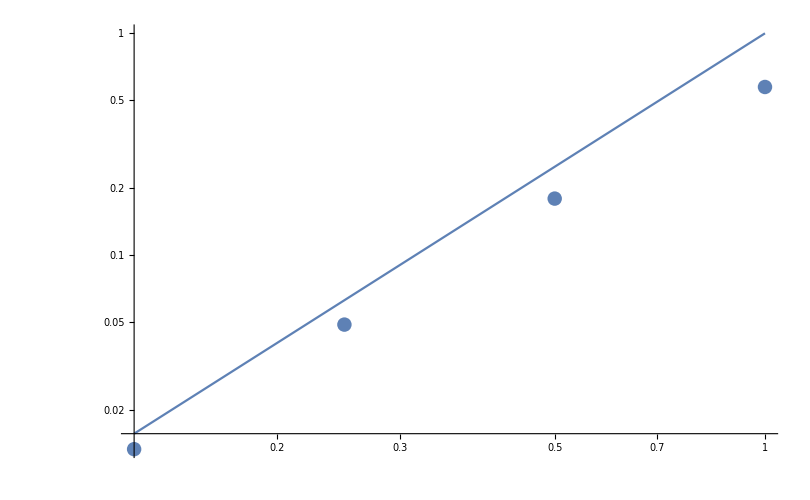

```mathematica
p1=LogLogPlot[{x^2},{x,0.125,1}];
conv0={{1,0.5726597178391083},{0.5,0.17962498401837718},{0.25,0.048522113154471073},{0.125,0.013301431509308907}};
conv1={{1,0.7400348682737291},{0.5,0.8512272994883749},{0.25,0.032763480454977435},{0.125,0.008660723698336644}};

p2=ListLogLogPlot[{conv0}];
Show[p1,p2,PlotRange->All]
```

```mathematica
allPoints=Join[xFacePosS,xFacePos];
zero=allPoints[[lookupface[3,1,3]]];
For[ii=1,ii<=Length[allPoints],ii++,
allPoints[[ii]]=allPoints[[ii]]-zero;
]
fancyFunction[x_,y_,z_]=(x+2)^2+1+Cos[5x];
realLaplacian[x_,y_,z_]=D[fancyFunction[0,y,0],{y,2}];
allVals=Table[fancyFunction[allPoints[[ii,1]],allPoints[[ii,2]],allPoints[[ii,3]]],{ii,1,Length[allPoints]}];

discreteLap=16/21 allVals[[lookupfaceS[5,4,5]]]/delta^2+16/21 allVals[[lookupfaceS[5,4,6]]]/delta^2-8/3 allVals[[lookupface[3,1,3]]]/delta^2+8/7 allVals[[lookupface[3,2,3]]]/delta^2
realLaplacian[0,0,0]
-(discreteLap-realLaplacian[0,0,0])/realLaplacian[0,0,0]
```

-123.

0

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(*inter[y_]=(8 y (-1+y/delta))/(21 delta) allVals[[lookupfaceS[5,4,5]]]+(8 y (-1+y/delta))/(21 delta) allVals[[lookupfaceS[5,4,6]]]+(1-y/delta-(4 y (-1+y/delta))/(3 delta)) allVals[[lookupface[3,1,3]]]+(y/delta+(4 delta (-1+y/delta))/(7 delta))  allVals[[lookupface[3,2,3]]]
*)
inter[y_]=(8 y (-1+y/delta))/(21 delta) allVals[[lookupfaceS[5,4,5]]]+(8 y (-1+y/delta))/(21 delta) allVals[[lookupfaceS[5,4,6]]]+(1-y/delta-(4 y (-1+y/delta))/(3 delta)) allVals[[lookupface[3,1,3]]]+(y/delta+(4  y(-1+y/delta))/(7 delta))  allVals[[lookupface[3,2,3]]];

points={{allPoints[[lookupfaceS[5,4,5],2]],allVals[[lookupfaceS[5,4,5]]]},{allPoints[[lookupfaceS[5,4,6],2]],allVals[[lookupfaceS[5,4,6]]]},{allPoints[[lookupface[3,1,3],2]],allVals[[lookupface[3,1,3]]]},{allPoints[[lookupface[3,2,3],2]],allVals[[lookupface[3,2,3]]]}};
D[inter[y],{y,2}]
```

-22.9934

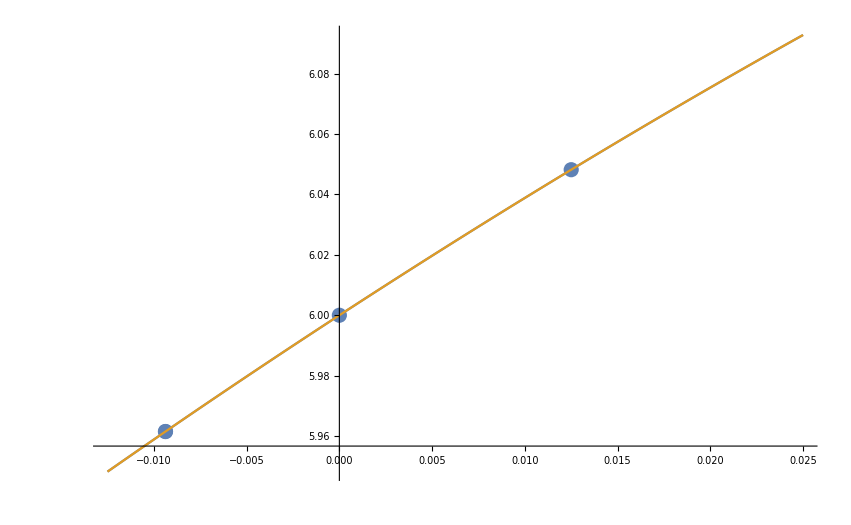

```mathematica
p1=ListPlot[points];
p2=Plot[{inter[y],fancyFunction[0,y,0]},{y,-delta,2delta},PlotRange->All];
Show[p1,p2,PlotRange->All]
```